```mathematica
K2meV=0.086173324;
K2eV=K2meV/1000;
SetDirectory["/Volumes/MicroSD/Dropbox/RESULTS_tom_26Jun17/SUBSTOI"];
fileFFE={"e0.out","e0_fs.out","VFE.Fqh_FS.out.m","VFE.Fel_Fqh_FS.out.m"};
FFEdata=Table[ReadList[fileFFE[[i]],{Number, Number,Number,Number,Number}],{i,1,4}];
```

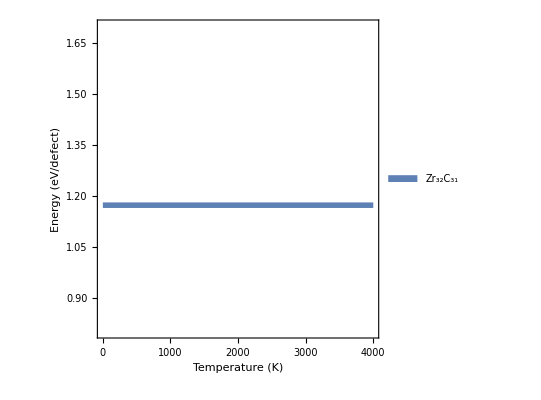

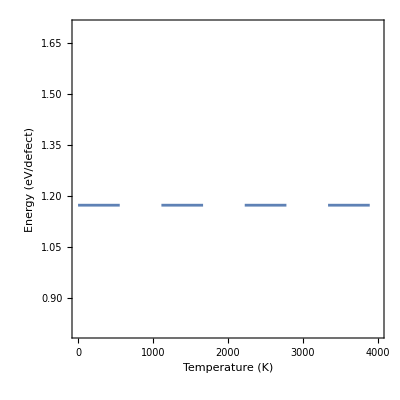

```mathematica
G1=ListLinePlot[Transpose[FFEdata[[1]]][[4]],PlotRange->{Automatic,{0.8,1.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["Zr_32C_31",20,Black]}]]
G1a=ListLinePlot[Transpose[FFEdata[[1]]][[4]],PlotRange->{Automatic,{0.8,1.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.075]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

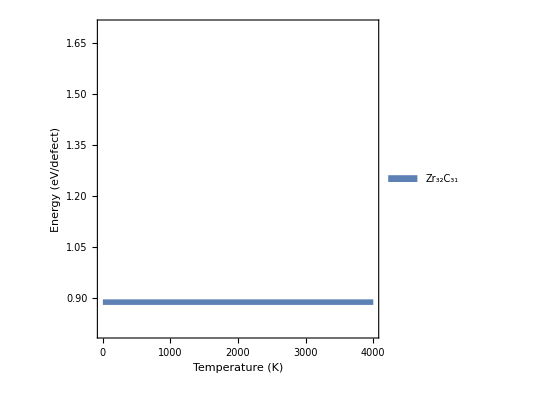

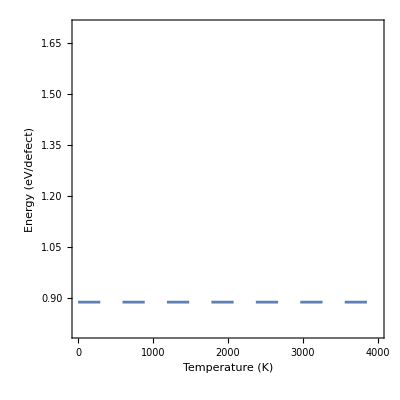

```mathematica
G2=ListLinePlot[Transpose[FFEdata[[2]]][[4]],PlotRange->{Automatic,{0.8,1.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["Zr_32C_31",20,Black]}]]
G2a=ListLinePlot[Transpose[FFEdata[[2]]][[4]],PlotRange->{Automatic,{0.8,1.7}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Directive[Thickness[0.005],Dashing[0.04]],FrameTicksStyle->18,Frame->True,ImageSize->400]
```

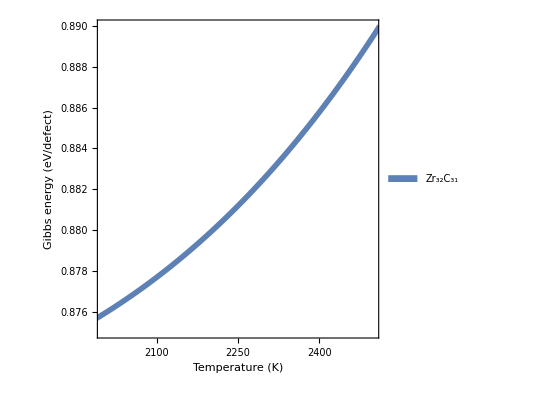

```mathematica
G4=ListLinePlot[Transpose[FFEdata[[4]]][[4]],PlotRange->{{2000,2500},{0.875,0.89}},FrameLabel->{Style["Temperature (K)",18,Black],Style["Gibbs energy (eV/defect)",18,Black]},AspectRatio->1,FrameStyle->Directive[Black,Thickness[0.01]],PlotStyle->Thickness[0.01],FrameTicksStyle->18,Frame->True,ImageSize->400,PlotLegends->SwatchLegend[{Style["Zr_32C_31",20,Black]}]]
```

```mathematica
gibbsData=FFEdata[[4]];
temperature=Transpose[gibbsData][[1]];
gibbsCVAC=Transpose[gibbsData][[2]];
```

```mathematica
upper=3500;
lower=2000;
rangeT=temperature[[lower;;upper]];
rangeGibbsCVAC=gibbsCVAC[[lower;;upper]];
concCVAC=Transpose@{rangeT,100*Exp[-(rangeGibbsCVAC)/(K2eV*rangeT)]};
```

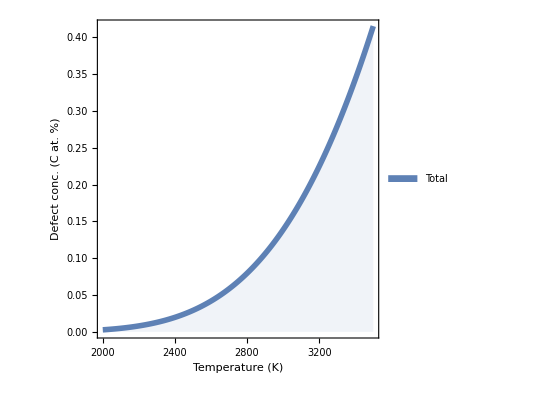

```mathematica
p7=ListLinePlot[concCVAC,PlotStyle->Thickness[0.01],Filling->Bottom,FrameStyle->Directive[Thickness[0.01]],FillingStyle->Opacity[0.09],FrameTicksStyle->Directive[18,Black],FrameLabel->{Style["Temperature (K)",18,Black],Style["Defect conc. (C at. %)",18,Black]},Frame->True,ImageSize->400,PlotLegends->Placed[SwatchLegend[{Style["Total",18,Black]}],{0.3,0.75}],AspectRatio->1,PlotRange->{Automatic,Automatic}]
```